```mathematica
f = lw+pw^3 (2/(n bc^4)+(b g)/(2 n bc^3))+pw (-g-2/(n bc^2)+(b g)/bc-(b g)/(2 n bc))
```

lw+(-g+(b g)/bc-2/(bc^2 n)-(b g)/(2 bc n)) pw+(2/(bc^4 n)+(b g)/(2 bc^3 n)) pw^3

```mathematica
R = Solve[f==0,pw];
r1 = R[[1]][[1]];
r2 = R[[2]][[1]];
r3 = R[[3]][[1]];
(*Roots for free field case*)
rr1 = pw/.r1;
rr2 = pw/.r2;
rr3 =pw/.r3;

rb1 = Simplify[rr1,{g>0,bc>0,n>0}];
rb2 = Simplify[rr2,{g>0,bc>0,n>0}];
rb3 = Simplify[rr3,{g>0,bc>0,n>0}];
```

```mathematica
f1 = pw^3 (2/(n bc^4)+(b g)/(2 n bc^3))+pw (-2/(n bc^2)-(b g)/(2 n bc))
R1= Solve[f1==0,pw];
r11 = R1[[1]][[1]];
r12 = R1[[2]][[1]];
r13 = R1[[3]][[1]];
(*Roots for free field case*)
rr11 = pw/.r11;
rr12 = pw/.r12;
rr13 =pw/.r13;
Solve[{f1/.pw-> -lw/(-g+(b g)/bc)}== 0,b]
```

(-2/(bc^2 n)-(b g)/(2 bc n)) pw+(2/(bc^4 n)+(b g)/(2 bc^3 n)) pw^3

{{b→-4/(bc g)},{b→(bc g-lw)/g},{b→(bc g+lw)/g}}

```mathematica
l1 = Limit[rb1,n->∞];
l2 = Limit[rb2,n->∞];
l3 = Limit[rb3,n->∞];
```

This behavior suggests that the susceptibility near the critical point behaves as (b-bx)^(-1/2), which suggests the critical exponent associated with it is 1/2; These values for the critical exponents are expected, as the expression for energy we have is effectively a mean field approximation of the vertex model. This suggests the dynamic change in wound area evolution is intrinsically connected with the state properties of the tissue, and for a free-field case (in the absence of actin-myosin tension) the closure process can occur if the tissue is in a fluid-like state, with the critical point for the parameter b corresponding to the critical parameter p0 in the classical vertex model phase diagram by Staple et al (for the thermodynamic limit as n approaches infinity).

```mathematica
Collect[FactorTerms[lw/.Solve[Simplify[f/.pw-> Sqrt[k]bc]==0,lw][[1]][[1]],b],n]
```

1/2 (-2 b g √k+2 bc g √k)+((4 √k)/bc+b g √k-(4 k^(3/2))/bc-b g k^(3/2))/(2 n)

```mathematica
rfixed1 = rb1/.n->10^2/.g-> 1/.bc-> 1/Sqrt[ 1/(8 √3)]/.m-> 1;
rfixed3 = rb3/.n-> 10^2/.g-> 1/.bc-> 1/Sqrt[ 1/(8 √3)]/.m-> 1;
rdiff = rfixed1-rfixed3;
ListRootsdf1= {};
For[bq=10,bq<100,bq++,rootbq = rdiff/.n-> 100/.g-> 1/.r-> 1/(2Sqrt[Pi])/.b->(bq/20);AppendTo[ListRootsdf1,{bq/20,lw/.FindRoot[rootbq,{lw,30}]}]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

```mathematica
nlm1 = NonlinearModelFit[Re[ListRootsdf1[[1;;58]]],a^2 x^2 + b^2 +2 a b x, {a,b}, x];
```

```mathematica
Normal[nlm1]
 x/.Flatten[{Solve[ Reduce[Roots[Normal[nlm1]==0,x]],{x},Reals]}]
```

32.9936-17.4188 x+2.29905 x^2

3.78827

```mathematica
32.993567758858426-17.418817628940108 (x-3.7)+2.2990481796926225 (x-3.7)^2
```

32.9936-17.4188 (-3.7+x)+2.29905 (-3.7+x)^2

```mathematica
lm2[y_]:=32.9936-17.418817628940108 (3.7882672017923875-y)+2.2990481796926225 (3.7882672017923875-y)^2
```

```mathematica
Sqrt[2.2990481796926225]
```

1.51626

Contour Plot of pw in function of beta and lambda

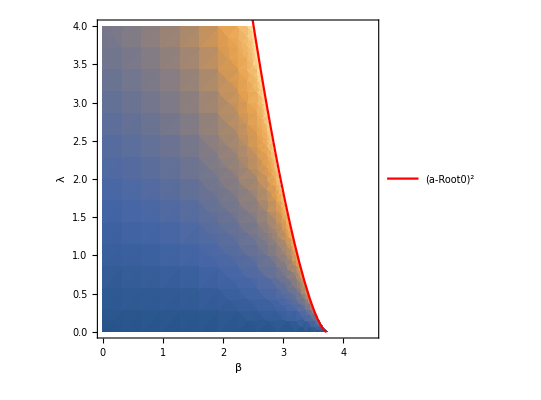

```mathematica
p1 = DensityPlot[Chop[rfixed3],{b,0,4.5},{lw,0,4},FrameLabel-> {Style[β,16],Style[λ,16]}];
p2 = Plot[3(3.72-b)^{3/2},{b,0.5,4.5},PlotStyle-> Red,PlotLegends->{(a-x)^2/.x-> Root0}];
Show[p1,p2]
```

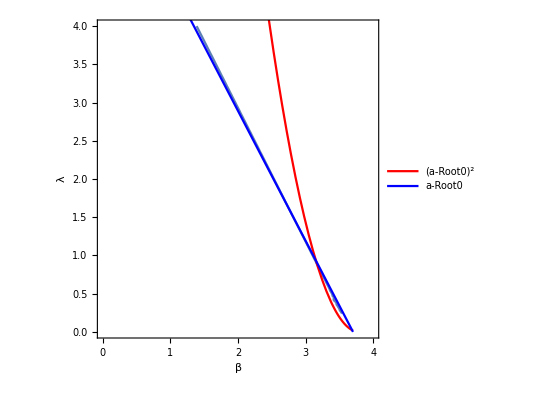

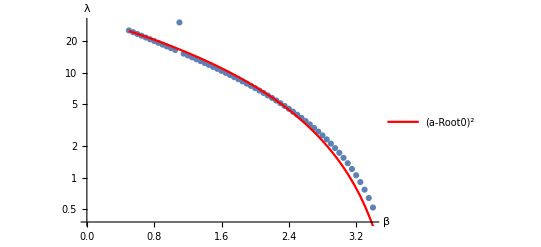

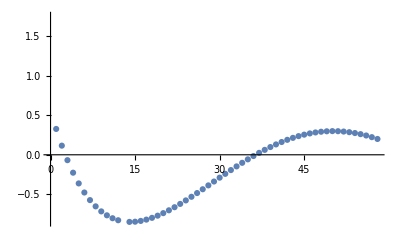

```mathematica
p1 = ContourPlot[Chop[rfixed3^2* 1/(8 √3)]==3,{b,0,4},{lw,0,4},FrameLabel-> {Style[β,16],Style[λ,16]}];
p2 = Plot[nlm1[b],{b,0.5,3.7},PlotStyle-> Red,PlotLegends->{(a-x)^2/.x-> Root0}];
p3 = Plot[1.7(3.7 - b),{b,0,3.7},PlotStyle-> Blue,PlotLegends->{(a-x)/.x-> Root0}];
Show[p1,p2,p3]
Show[ListLogPlot[Re[ListRootsdf1[[1;;59]]]],LogPlot[nlm1[b],{b,0.5,3.7},PlotStyle-> Red,PlotLegends->{(a-x)^2/.x-> Root0}],AxesLabel-> {Style[β,16],Style[λ,16]}]
ListPlot[nlm1["FitResiduals"]]
```

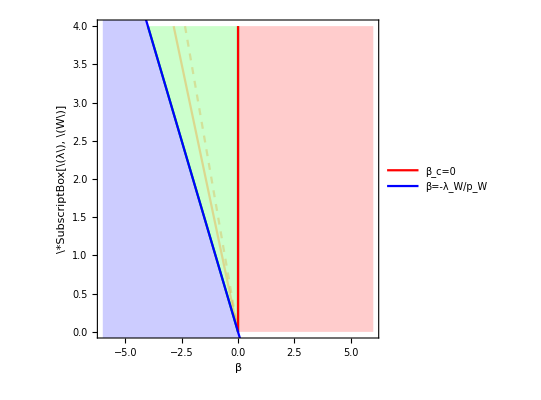

```mathematica
p1 = Plot[{-b,10^10(-b)},{b,-6,6},PlotStyle-> Green,Filling-> {Bottom,1->{2}},PlotRange->{{-6,6},{0,4}},Frame-> True,PlotStyle->{{Black,Thick}},BaseStyle->{FontSize->20,FontFamily->"Times"},LabelStyle->{FontSize->20,FontFamily->"Times",Black}];
p2 = Plot[{1.4(-b),1.7(-b)},{b,-6,6},PlotStyle->{{Orange,Opacity[0.3]},{Dashed,Opacity[0.3]}},PlotRange->{{-6,6},{0,4}},Frame->True];
p3 = Plot[{10^10(-b)},{b,-6,6},PlotStyle-> Red,PlotLegends->{"β_c=0"},Filling-> Top,PlotRange->{{-6,6},{0,4}}];
p4 = Plot[-b,{b,-6,6},PlotStyle-> Blue,PlotLegends->{"β=-λ_W/p_W"},Filling-> Bottom];
Show[p1,p2,p3,p4,FrameLabel->{"β","\*SubscriptBox[\(λ\), \(W\)]"},AspectRatio->1]
```

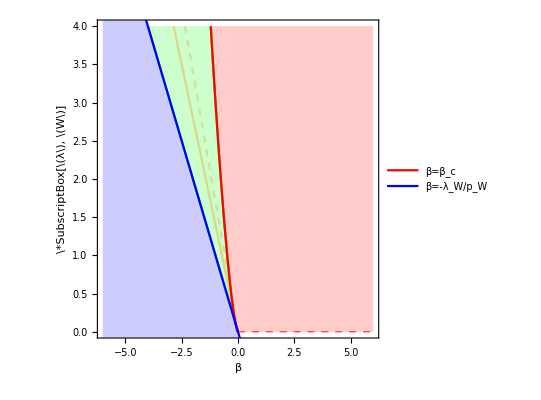

```mathematica
p1 = Plot[{-b,3*(-b)^{3/2}},{b,-6,0},PlotStyle-> Green,Filling-> {Bottom,1->{2}},PlotRange->{{-6,6},{0,4}},Frame-> True,PlotStyle->{{Black,Thick}},BaseStyle->{FontSize->20,FontFamily->"Times"},LabelStyle->{FontSize->20,FontFamily->"Times",Black}];
p2 = Plot[{1.4(-b),1.7(-b)},{b,-6,6},PlotStyle->{{Orange,Opacity[0.3]},{Dashed,Opacity[0.3]}},PlotRange->{{-6,6},{0,4}},Frame->True];
p3 = Plot[{3*(-b)^{3/2}},{b,-6,0},PlotStyle-> Red,PlotLegends->{"β=β_c"},Filling-> Top,PlotRange->{{-6,6},{0,4}}];
p4 = Plot[-b,{b,-6,6},PlotStyle-> Blue,PlotLegends->{"β=-λ_W/p_W"},Filling-> Bottom];
p5 = Plot[{0},{b,0,6},PlotStyle-> {Red,Dashed,Thickness[0.001]},Filling->{Bottom},PlotRange->{{-6,6},{0,4}}];
p6 = Plot[{0},{b,0,6},PlotStyle-> {Red,Dashed,Thickness[0.001]},Filling->{Top},PlotRange->{{-6,6},{0,4}}];
Show[p1,p2,p3,p4,p5,p6,FrameLabel->{"β","\*SubscriptBox[\(λ\), \(W\)]"},AspectRatio->1]
```

```mathematica
N[Sqrt[4 n Tan[π/n]]/.n-> 6]
```

3.72242